```mathematica
convergenceData[file_]:=Module[
{raw},
raw=ReadList[NotebookDirectory[]<>file,{Number,Number, Number, Number}];
{
{#[[1]],#[[2]]}&/@raw,
{#[[1]],#[[3]]}&/@raw,
{#[[1]],#[[4]]}&/@raw
}
];
```

```mathematica
convInput2Spec400Bc1Bus300=convergenceData["convergence_input2_400spec_bc1_300buses.txt"];
convInput2Spec400Bc1Bus30=convergenceData["convergence_input2_400spec_bc1_30buses.txt"];
convInput2Spec40Bc1Bus300=convergenceData["convergence_input2_40spec_bc1_300buses.txt"];
convInput4Spec400Bc10Bus100=convergenceData["convergence_input4_400spec_bc10_100buses.txt"];
convInput4Spec400Bc1Bus1000=convergenceData["convergence_input4_400spec_bc1_1kbuses.txt"];
convInput4Spec40Bc1Bus1000=convergenceData["convergence_input4_40spec_bc1_1kbuses.txt"];
convRandom0Spec100Bc1Bus10000=convergenceData["convergence_random0_100spec_bc1_10kbuses.txt"];
convRandom0Spec500Bc1Bus1000=convergenceData["convergence_random0_500spec_bc10_1kbuses.txt"];
convRandom0Spec500Bc1Bus10000=convergenceData["convergence_random0_500spec_bc1_10kbuses.txt"];
```

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->14}];
makePlot[data_,label_]:=ListPlot[data,PlotLegends->{"Min","Max","Avg"},AxesLabel->{"Iterations","Fitness"},AxesOrigin->{0,0},
PlotMarkers->{{●,15},{▲,15},{■,15}},PlotLabel->label];
```

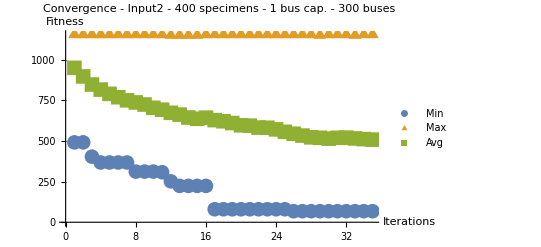

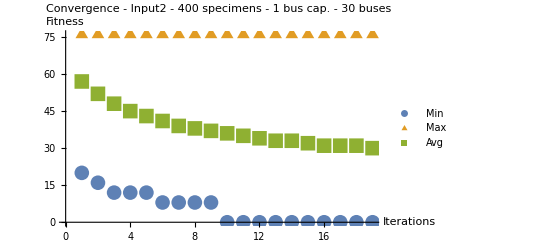

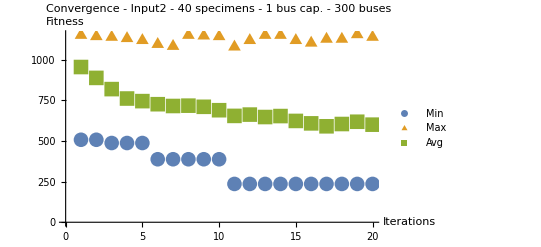

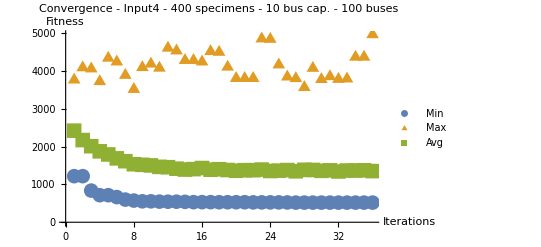

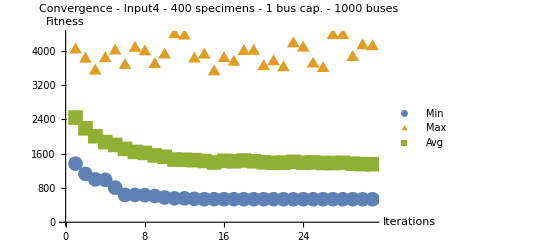

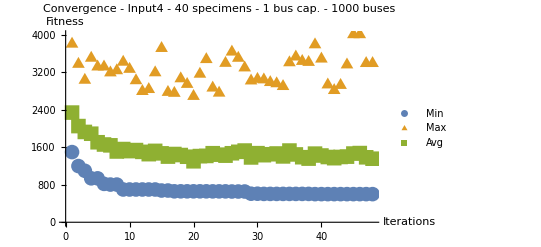

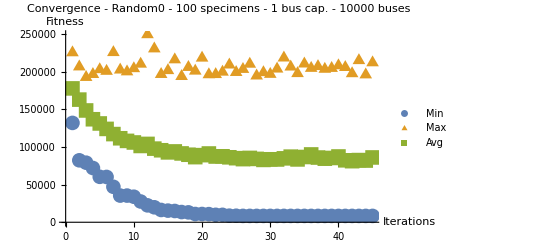

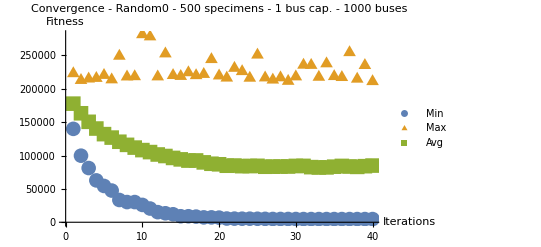

```mathematica
makePlot[convInput2Spec400Bc1Bus300,"Convergence - Input2 - 400 specimens - 1 bus cap. - 300 buses"]
makePlot[convInput2Spec400Bc1Bus30,"Convergence - Input2 - 400 specimens - 1 bus cap. - 30 buses"]
makePlot[convInput2Spec40Bc1Bus300,"Convergence - Input2 - 40 specimens - 1 bus cap. - 300 buses"]
makePlot[convInput4Spec400Bc10Bus100,"Convergence - Input4 - 400 specimens - 10 bus cap. - 100 buses"]
makePlot[convInput4Spec400Bc1Bus1000,"Convergence - Input4 - 400 specimens - 1 bus cap. - 1000 buses"]
makePlot[convInput4Spec40Bc1Bus1000,"Convergence - Input4 - 40 specimens - 1 bus cap. - 1000 buses"]
makePlot[convRandom0Spec100Bc1Bus10000,"Convergence - Random0 - 100 specimens - 1 bus cap. - 10000 buses"]
makePlot[convRandom0Spec500Bc1Bus1000,"Convergence - Random0 - 500 specimens - 1 bus cap. - 1000 buses"]
makePlot[convRandom0Spec500Bc1Bus10000,"Convergence - Random0 - 500 specimens - 1 bus cap. - 10000 buses"]
```